## Definiciones

```mathematica
circle3D[centre_:{0,0,0},radius_:1,normal_:{0,0,1},angle_:{0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle>=2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]]
```

## Idea general:

Los PCE se pueden extender y agregar también las fases.

## Esfera de Bloch

La idea es describir también reflexiones de estados como:

```mathematica
Graphics3D[{{Red,Arrowheads[0.03],Arrow[Tube[{{0,0,0},{-1,1,1}/√3},0.01]]},{Black,Arrowheads[0.03],Arrow[Tube[{{0,0,0},{-1/√3,0,0}},0.015]]},{Green,Arrowheads[0.03],Arrow[Tube[{{-1/√3,0,0},{-1/√3,1/√3,0}},0.015]]},
{Blue,Arrowheads[0.01],Arrow[Tube[{{-1,1,0},{-1,1,0.6}}/√3,0.01]]},{circle3D[{0,0,0},1,{1,0,0}]},{circle3D[{0,0,0},1,{0,0,1}]},{Opacity[0.3],Sphere[]},{Style[Text["ψ_0",{{-1,1,1}/√3+0.1}],Bold]}},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{x,y,z},LabelStyle->Directive[Black, FontSize->15,FontFamily->"Helvetica"],AxesStyle->{Thick,Thick,Thick},Ticks->None,Boxed->False]
```

-Graphics3D-

```mathematica
Graphics3D[{{Red,Arrowheads[0.03],Arrow[Tube[{{0,0,0},{1,0,0}/√3},0.015]]},{Opacity[0.3],EdgeForm[{Thick,Dashed,Blue}],Ellipsoid[{0,0,0},{1,0.1,0.1}]},{Opacity[0],Sphere[]},{Style[Text["ψ_f",{{1,0,0}/√3+0.25}],Bold]}},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{x,y,z},LabelStyle->Directive[Black, FontSize->15,FontFamily->"Helvetica"],AxesStyle->{Thick,Thick,Thick},Ticks->None,Boxed->False]
```

-Graphics3D-

## 1 qubit

```mathematica
s=ReplacePart[#,Position[#,-1]->0]&[A[{2}]]
```

{{1,1,1,1},{1,1,0,0},{1,0,1,0},{1,0,0,1}}

```mathematica
realG=DeleteDuplicates[Flatten[Table[A[{2}][[i]]#&/@s,{i,4}],1]]
```

{{1,1,1,1},{1,1,0,0},{1,0,1,0},{1,0,0,1},{1,1,-1,-1},{1,0,-1,0},{1,0,0,-1},{1,-1,1,-1},{1,-1,0,0},{1,-1,-1,1}}

```mathematica
MatrixForm/@realG
```

{(1
1
1
1),(1
1
0
0),(1
0
1
0),(1
0
0
1),(1
1
-1
-1),(1
0
-1
0),(1
0
0
-1),(1
-1
1
-1),(1
-1
0
0),(1
-1
-1
1)}

Estos puntos son

```mathematica
Graphics3D[{{Opacity[.25],Tetrahedron[{{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}},VertexColors->{Blue,Pink,Blue,White}]},{PointSize[0.025],Red,Point[{{1,0,0},{0,1,0},{0,0,1},{-1,0,0},{0,-1,0},{0,0,-1}}]},{Thickness[0.005],{Line[{{0,0,1},{0,1,0}}],Line[{{0,1,0},{1,0,0}}]},Line[{{1,0,0},{0,0,1}}],Line[{{0,0,1},{-1,0,0}}],Line[{{0,0,1},{0,-1,0}}],Line[{{1,0,0},{0,-1,0}}],Line[{{1,0,0},{0,0,-1}}],Line[{{0,1,0},{-1,0,0}}],Line[{{0,1,0},{0,0,-1}}],Line[{{0,-1,0},{-1,0,0}}],Line[{{0,-1,0},{0,0,-1}}],Line[{{0,0,-1},{-1,0,0}}]},Text[Style["(1,1,1)",FontSize->14,FontFamily->"Bitstream Vera Sans Mono"],{1.1,1.1,1.1}],Text[Style["λ_(1,2,3) = (1,-1,-1)",FontSize->14,FontFamily->"Bitstream Vera Sans Mono"],{0.7,-1,-1.1}],Text[Style["(-1,1,-1)",FontSize->14,FontFamily->"Bitstream Vera Sans Mono"],{-1.4,1.15,-0.8}],Text[Style["(-1,-1,1)",FontSize->14,FontFamily->"Bitstream Vera Sans Mono"],{-1.1,-1.1,1}],Text[Style["(1,0,0)",FontSize->14,FontFamily->"Bitstream Vera Sans Mono"],{1.3,0.2,0}],Text[Style["(0,1,0)",FontSize->14,FontFamily->"Bitstream Vera Sans Mono"],{0.4,0.8,0}],Text[Style["(0,0,1)",FontSize->14,FontFamily->"Bitstream Vera Sans Mono"],{-0.1,0,1.25}],
Text[Style["(-1,0,0)",FontSize->14,FontFamily->"Bitstream Vera Sans Mono"],{-1.1,0,0}],Text[Style["(0,-1,0)",FontSize->14,FontFamily->"Bitstream Vera Sans Mono"],{0,-1.1,0}],Text[Style["(0,0,-1)",FontSize->14,FontFamily->"Bitstream Vera Sans Mono"],{0,0,-1.1}]},Boxed->False,ImageSize->500]
```

-Graphics3D-

```mathematica
s=ReplacePart[#,Position[#,-1]->0]&[A[{2,2}]]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,0,0,0,0,1,1,1,1,0,0,0,0},{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0},{1,1,1,1,0,0,0,0,0,0,0,0,1,1,1,1},{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0},{1,0,1,0,0,1,0,1,1,0,1,0,0,1,0,1},{1,0,1,0,1,0,1,0,0,1,0,1,0,1,0,1},{1,0,1,0,0,1,0,1,0,1,0,1,1,0,1,0},{1,1,0,0,1,1,0,0,1,1,0,0,1,1,0,0},{1,1,0,0,0,0,1,1,1,1,0,0,0,0,1,1},{1,1,0,0,1,1,0,0,0,0,1,1,0,0,1,1},{1,1,0,0,0,0,1,1,0,0,1,1,1,1,0,0},{1,0,0,1,1,0,0,1,1,0,0,1,1,0,0,1},{1,0,0,1,0,1,1,0,1,0,0,1,0,1,1,0},{1,0,0,1,1,0,0,1,0,1,1,0,0,1,1,0},{1,0,0,1,0,1,1,0,0,1,1,0,1,0,0,1}}

```mathematica
realG=DeleteDuplicates[Flatten[Table[ArrayReshape[#,{4,4}]&/@(A[{2,2}][[i]]#&/@s),{i,16}],1]];
```

```mathematica
16*16
```

256

```mathematica
Length[realG]
```

136

```mathematica
12*12
```

144

```mathematica
GraphicsGrid[ArrayReshape[MatrixPlot[#,ImageSize->Tiny,FrameTicks->None]&/@realG,{12,12}]]
```

-Graphics-

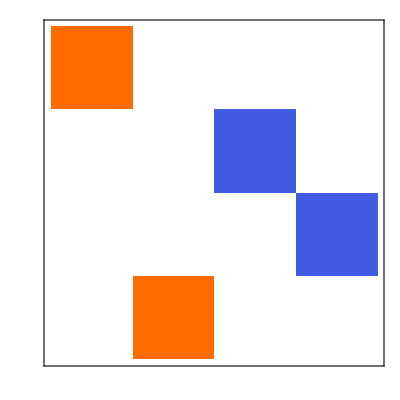
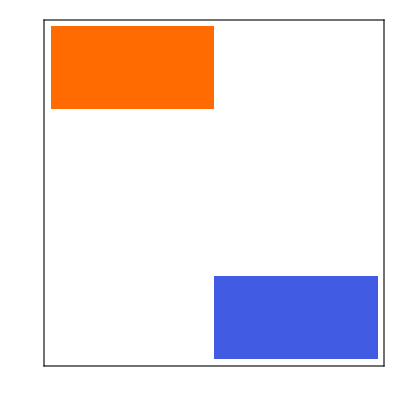
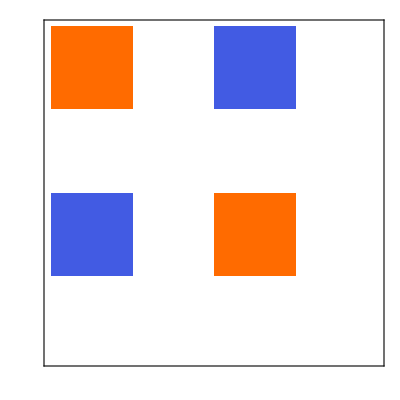
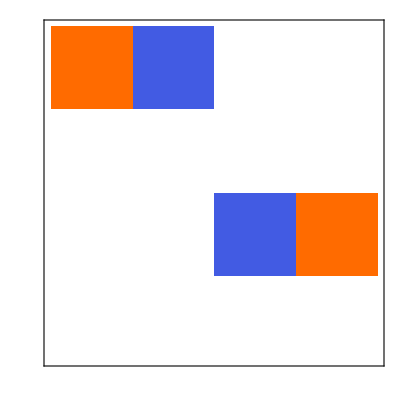
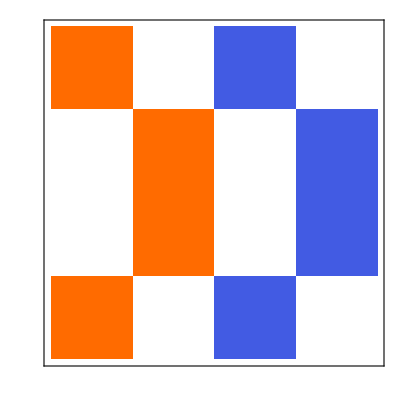
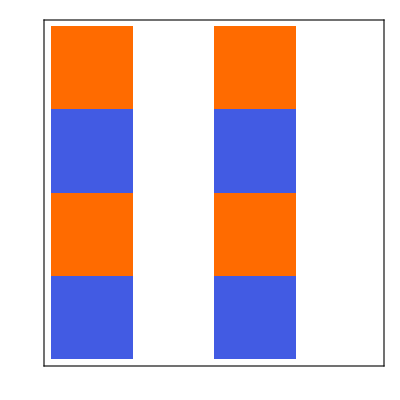
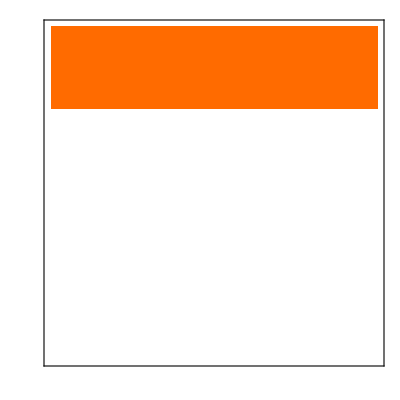
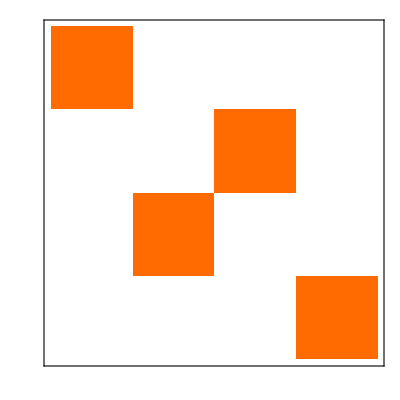

```mathematica
SeedRandom[341321];Table[MatrixPlot[#[[RandomInteger[{1,136}]]]#[[RandomInteger[{1,136}]]]&[realG],FrameTicks->None],10]
```

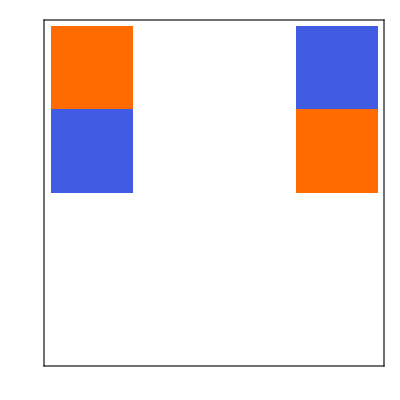
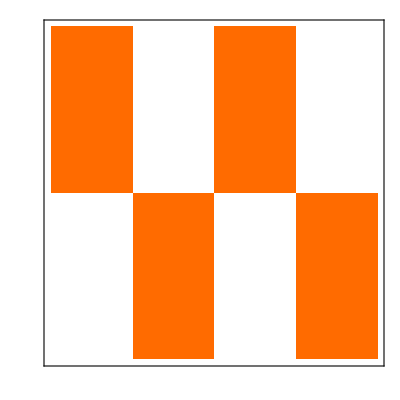
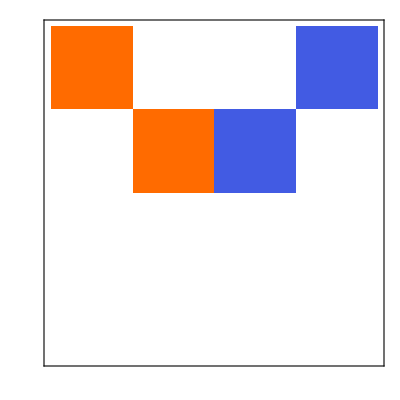
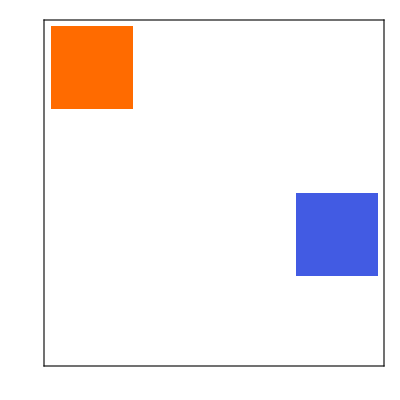
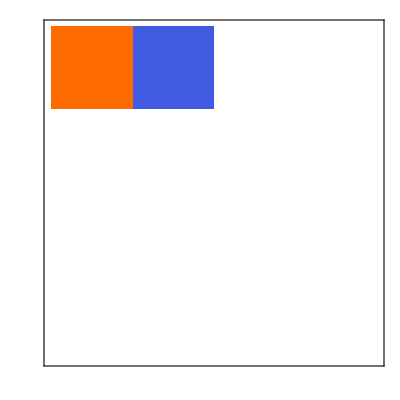
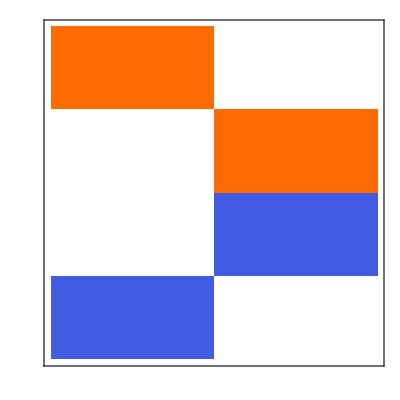
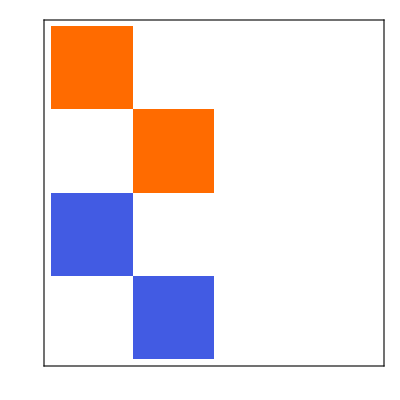
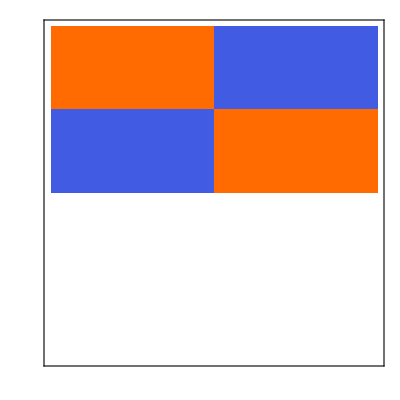
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[3321];Table[MatrixPlot[#[[RandomInteger[{1,136}]]]#[[RandomInteger[{1,136}]]]#[[RandomInteger[{1,136}]]]&[realG],FrameTicks->None],10]
```

```mathematica
realG//Length
```

10